#### Import MGenPackage

```mathematica
Block[{$Path=Append[$Path,NotebookDirectory[]]},
<<MGenPackage`]
```

#### Try to learn a simple stochastic sequence

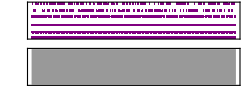

```mathematica
midi=Import[FileNameJoin[{NotebookDirectory[],"chords.mid"}]]
```

```mathematica
noteString=polyphonicMIDIToString[FileNameJoin[{NotebookDirectory[],"chords.mid"}]];
```

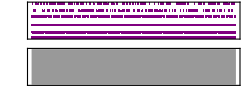

```mathematica
stringToSound[noteString,120]
```

```mathematica
text=noteString;
trainingdata=sampleText[text,150,20000];
RandomSample[trainingdata,5]
generator=Function[sampleText[text,150,#BatchSize]];
```

{++++++++      KOW+++++      HOT+++++++    H+++K+++T+++  W+++++++++++++++++    KO  W+++++++++++    HO  W+++++  H+++K+++T+++    [+++++  KO    W+++++  HO → ,+++++++      KO    W+++++  HO    [+++++++++++H+++K+++T+++      [+++++KO      HOW+++++++++++++++++    H+++K+++T+++  W+++++++++++    KO  W+++++    HO  T+→+,++T+++    [+++++++++++  KO    [+++++  HO    H+++K+++T+++W+++++      [+++++++++++++++++KO      [+++++++++++HO    H+++K+++T+++  [+++++    KO  T+++++    H→O,K+++T+++    W+++++++++++  KO    W+++++  HO    [+++++H+++K+++T+++      KOT+++++++++++++      HOT+++++++    H+++K+++T+++  [+++++    KO  W+++++++++++    H→O,++T+++      KOW+++++      [+++++HO    H+++K+++T+++  T+    KO  W+++++    HO  [+++++  H+++K+++T+++++++++      KO    W+++++  HO    [+++++H+++K+++T+++     → }

```mathematica
net6=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[30,"Dropout"->0.2],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

```mathematica
trained6=net6;
```

```mathematica
trained6=NetTrain[trained6,trainingdata,BatchSize->512,TargetDevice->"CPU",MaxTrainingRounds->Quantity[8,"Hours"],TrainingProgressCheckpointing->{"Directory","~/Desktop/slask/SimpleChordsCheckpoints"}]
```

NetChain[]

#### Success. The net learned the sequence.

```mathematica
trained6=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-14T20:47:04_5_098_03881_2.16e-1.wlnet"}]]
```

NetChain[]

```mathematica
toWAVSound[stringToSound[string=generateSample[trained6,"HOT+++++++",1000],120.]]
```